# CS 478

## Scott Leland Crossen

## Clustering (KMeans) Project

### Part 1

The code that implements the kmeans clustering algorithm is included with the submission of this project. It is written in Scala and follows the functional paradigm. The output for k=4 clusters on the sponge dataset is shown below:

#### Expand for Full Output

***************
Iteration 1
***************
Centroid 0 = 1_CAPA, SIN_CAPA_INTERNA_DEL_CORTEX, SI, 3.000, SIN_TILOSTILOS_ADICIONALES, SIN_ESPICULA_PRINCIPAL_ESTILO, 3.000, 0.000, OTROS
Centroid 1 = SIN_CORTEX, SIN_CAPA_INTERNA_DEL_CORTEX, NO, 0.000, SIN_TILOSTILOS_ADICIONALES, SIN_ESPICULA_PRINCIPAL_ESTILO, 1.000, 0.000, ?
Centroid 2 = SIN_CORTEX, SIN_CAPA_INTERNA_DEL_CORTEX, NO, 0.000, SIN_TILOSTILOS_ADICIONALES, SIN_ESPICULA_PRINCIPAL_ESTILO, 1.000, 1.000, OTROS
Centroid 3 = SIN_CORTEX, SIN_CAPA_INTERNA_DEL_CORTEX, NO, 0.000, SIN_TILOSTILOS_ADICIONALES, SIN_ESPICULA_PRINCIPAL_ESTILO, 1.000, 3.000, OTROS
Amount of instances: Cluster 0: 39, Cluster 1: 30, Cluster 2: 3, Cluster 3: 4
Individual SSE: Cluster 0: 299.000, Cluster 1: 87.000, Cluster 2: 9.000, Cluster 3: 49.000
Total SSE: 444.000

***************
Iteration 2
***************
Centroid 0 = 2_CAPAS, TANGENCIAL, SI, 2.821, SIN_TILOSTILOS_ADICIONALES, SIN_ESPICULA_PRINCIPAL_ESTILO, 2.590, 1.462, OTROS
Centroid 1 = SIN_CORTEX, SIN_CAPA_INTERNA_DEL_CORTEX, NO, 0.000, SIN_TILOSTILOS_ADICIONALES, SIN_ESPICULA_PRINCIPAL_ESTILO, 1.933, 0.000, OTROS
Centroid 2 = SIN_CORTEX, SIN_CAPA_INTERNA_DEL_CORTEX, NO, 0.667, SIN_TILOSTILOS_ADICIONALES, SIN_ESPICULA_PRINCIPAL_ESTILO, 0.667, 1.333, OTROS
Centroid 3 = 2_CAPAS, TANGENCIAL, SI, 2.000, ECTOSOMICOS_DISPERSOS, SIN_ESPICULA_PRINCIPAL_ESTILO, 2.250, 3.500, OTROS
Amount of instances: Cluster 0: 36, Cluster 1: 31, Cluster 2: 4, Cluster 3: 5
Individual SSE: Cluster 0: 169.375, Cluster 1: 53.404, Cluster 2: 7.667, Cluster 3: 23.063
Total SSE: 253.508

***************
Iteration 3
***************
Centroid 0 = 2_CAPAS, TANGENCIAL, SI, 2.861, SIN_TILOSTILOS_ADICIONALES, SIN_ESPICULA_PRINCIPAL_ESTILO, 2.528, 1.444, OTROS
Centroid 1 = SIN_CORTEX, SIN_CAPA_INTERNA_DEL_CORTEX, NO, 0.065, SIN_TILOSTILOS_ADICIONALES, SIN_ESPICULA_PRINCIPAL_ESTILO, 2.065, 0.000, OTROS
Centroid 2 = SIN_CORTEX, SIN_CAPA_INTERNA_DEL_CORTEX, NO, 0.000, SIN_TILOSTILOS_ADICIONALES, SIN_ESPICULA_PRINCIPAL_ESTILO, 0.500, 1.250, OTROS
Centroid 3 = 2_CAPAS, TANGENCIAL, SI, 3.000, INTERMEDIARIOS, FUSIFORME, 2.600, 3.600, AMARILLO_PALIDO
Amount of instances: Cluster 0: 33, Cluster 1: 31, Cluster 2: 4, Cluster 3: 8
Individual SSE: Cluster 0: 149.292, Cluster 1: 52.742, Cluster 2: 5.750, Cluster 3: 27.160
Total SSE: 234.944

***************
Iteration 4
***************
Centroid 0 = 2_CAPAS, TANGENCIAL, SI, 2.758, SIN_TILOSTILOS_ADICIONALES, SIN_ESPICULA_PRINCIPAL_ESTILO, 2.515, 1.303, OTROS
Centroid 1 = SIN_CORTEX, SIN_CAPA_INTERNA_DEL_CORTEX, NO, 0.065, SIN_TILOSTILOS_ADICIONALES, SIN_ESPICULA_PRINCIPAL_ESTILO, 2.065, 0.000, OTROS
Centroid 2 = SIN_CORTEX, SIN_CAPA_INTERNA_DEL_CORTEX, NO, 0.000, SIN_TILOSTILOS_ADICIONALES, SIN_ESPICULA_PRINCIPAL_ESTILO, 0.500, 1.250, OTROS
Centroid 3 = 2_CAPAS, TANGENCIAL, SI, 3.375, INTERMEDIARIOS, SIN_ESPICULA_PRINCIPAL_ESTILO, 2.625, 3.375, AMARILLO_PALIDO
Amount of instances: Cluster 0: 30, Cluster 1: 31, Cluster 2: 4, Cluster 3: 11
Individual SSE: Cluster 0: 132.994, Cluster 1: 52.742, Cluster 2: 5.750, Cluster 3: 37.141
Total SSE: 228.627

***************
Iteration 5
***************
Centroid 0 = 2_CAPAS, TANGENCIAL, SI, 2.700, SIN_TILOSTILOS_ADICIONALES, SIN_ESPICULA_PRINCIPAL_ESTILO, 2.533, 1.200, OTROS
Centroid 1 = SIN_CORTEX, SIN_CAPA_INTERNA_DEL_CORTEX, NO, 0.065, SIN_TILOSTILOS_ADICIONALES, SIN_ESPICULA_PRINCIPAL_ESTILO, 2.065, 0.000, OTROS
Centroid 2 = SIN_CORTEX, SIN_CAPA_INTERNA_DEL_CORTEX, NO, 0.000, SIN_TILOSTILOS_ADICIONALES, SIN_ESPICULA_PRINCIPAL_ESTILO, 0.500, 1.250, OTROS
Centroid 3 = 2_CAPAS, TANGENCIAL, SI, 3.364, INTERMEDIARIOS, SIN_ESPICULA_PRINCIPAL_ESTILO, 2.545, 3.091, AMARILLO_PALIDO
Amount of instances: Cluster 0: 27, Cluster 1: 31, Cluster 2: 4, Cluster 3: 14
Individual SSE: Cluster 0: 119.590, Cluster 1: 52.742, Cluster 2: 5.750, Cluster 3: 47.950
Total SSE: 226.032

***************
Iteration 6
***************
Centroid 0 = 1_CAPA, SIN_CAPA_INTERNA_DEL_CORTEX, SI, 2.667, SIN_TILOSTILOS_ADICIONALES, SIN_ESPICULA_PRINCIPAL_ESTILO, 2.556, 1.111, OTROS
Centroid 1 = SIN_CORTEX, SIN_CAPA_INTERNA_DEL_CORTEX, NO, 0.065, SIN_TILOSTILOS_ADICIONALES, SIN_ESPICULA_PRINCIPAL_ESTILO, 2.065, 0.000, OTROS
Centroid 2 = SIN_CORTEX, SIN_CAPA_INTERNA_DEL_CORTEX, NO, 0.000, SIN_TILOSTILOS_ADICIONALES, SIN_ESPICULA_PRINCIPAL_ESTILO, 0.500, 1.250, OTROS
Centroid 3 = 2_CAPAS, TANGENCIAL, SI, 3.286, INTERMEDIARIOS, SIN_ESPICULA_PRINCIPAL_ESTILO, 2.500, 2.857, AMARILLO_PALIDO
Amount of instances: Cluster 0: 22, Cluster 1: 31, Cluster 2: 4, Cluster 3: 19
Individual SSE: Cluster 0: 88.617, Cluster 1: 52.742, Cluster 2: 5.750, Cluster 3: 69.403
Total SSE: 216.512

***************
Iteration 7
***************
Centroid 0 = 1_CAPA, SIN_CAPA_INTERNA_DEL_CORTEX, SI, 2.591, SIN_TILOSTILOS_ADICIONALES, SIN_ESPICULA_PRINCIPAL_ESTILO, 2.545, 0.909, OTROS
Centroid 1 = SIN_CORTEX, SIN_CAPA_INTERNA_DEL_CORTEX, NO, 0.065, SIN_TILOSTILOS_ADICIONALES, SIN_ESPICULA_PRINCIPAL_ESTILO, 2.065, 0.000, OTROS
Centroid 2 = SIN_CORTEX, SIN_CAPA_INTERNA_DEL_CORTEX, NO, 0.000, SIN_TILOSTILOS_ADICIONALES, SIN_ESPICULA_PRINCIPAL_ESTILO, 0.500, 1.250, OTROS
Centroid 3 = 2_CAPAS, TANGENCIAL, SI, 3.211, INTERMEDIARIOS, SIN_ESPICULA_PRINCIPAL_ESTILO, 2.526, 2.632, AMARILLO_PALIDO
Amount of instances: Cluster 0: 21, Cluster 1: 29, Cluster 2: 4, Cluster 3: 22
Individual SSE: Cluster 0: 80.390, Cluster 1: 42.241, Cluster 2: 5.750, Cluster 3: 83.634
Total SSE: 212.016

***************
Iteration 8
***************
Centroid 0 = 1_CAPA, SIN_CAPA_INTERNA_DEL_CORTEX, SI, 2.524, SIN_TILOSTILOS_ADICIONALES, SIN_ESPICULA_PRINCIPAL_ESTILO, 2.571, 0.667, OTROS
Centroid 1 = SIN_CORTEX, SIN_CAPA_INTERNA_DEL_CORTEX, NO, 0.000, SIN_TILOSTILOS_ADICIONALES, SIN_ESPICULA_PRINCIPAL_ESTILO, 2.000, 0.000, OTROS
Centroid 2 = SIN_CORTEX, SIN_CAPA_INTERNA_DEL_CORTEX, NO, 0.000, SIN_TILOSTILOS_ADICIONALES, SIN_ESPICULA_PRINCIPAL_ESTILO, 0.500, 1.250, OTROS
Centroid 3 = 2_CAPAS, TANGENCIAL, SI, 3.045, INTERMEDIARIOS, SIN_ESPICULA_PRINCIPAL_ESTILO, 2.545, 2.545, OTROS
Amount of instances: Cluster 0: 19, Cluster 1: 29, Cluster 2: 4, Cluster 3: 24
Individual SSE: Cluster 0: 66.385, Cluster 1: 42.000, Cluster 2: 5.750, Cluster 3: 91.058
Total SSE: 205.193

***************
Iteration 9
***************
Centroid 0 = 1_CAPA, SIN_CAPA_INTERNA_DEL_CORTEX, SI, 2.474, SIN_TILOSTILOS_ADICIONALES, SIN_ESPICULA_PRINCIPAL_ESTILO, 2.632, 0.526, OTROS
Centroid 1 = SIN_CORTEX, SIN_CAPA_INTERNA_DEL_CORTEX, NO, 0.000, SIN_TILOSTILOS_ADICIONALES, SIN_ESPICULA_PRINCIPAL_ESTILO, 2.000, 0.000, OTROS
Centroid 2 = SIN_CORTEX, SIN_CAPA_INTERNA_DEL_CORTEX, NO, 0.000, SIN_TILOSTILOS_ADICIONALES, SIN_ESPICULA_PRINCIPAL_ESTILO, 0.500, 1.250, OTROS
Centroid 3 = 2_CAPAS, TANGENCIAL, SI, 3.042, INTERMEDIARIOS, SIN_ESPICULA_PRINCIPAL_ESTILO, 2.500, 2.500, OTROS
Amount of instances: Cluster 0: 18, Cluster 1: 29, Cluster 2: 4, Cluster 3: 25
Individual SSE: Cluster 0: 61.310, Cluster 1: 42.000, Cluster 2: 5.750, Cluster 3: 95.460
Total SSE: 204.520

***************
Iteration 10
***************
Centroid 0 = 1_CAPA, SIN_CAPA_INTERNA_DEL_CORTEX, SI, 2.444, SIN_TILOSTILOS_ADICIONALES, SIN_ESPICULA_PRINCIPAL_ESTILO, 2.611, 0.444, OTROS
Centroid 1 = SIN_CORTEX, SIN_CAPA_INTERNA_DEL_CORTEX, NO, 0.000, SIN_TILOSTILOS_ADICIONALES, SIN_ESPICULA_PRINCIPAL_ESTILO, 2.000, 0.000, OTROS
Centroid 2 = SIN_CORTEX, SIN_CAPA_INTERNA_DEL_CORTEX, NO, 0.000, SIN_TILOSTILOS_ADICIONALES, SIN_ESPICULA_PRINCIPAL_ESTILO, 0.500, 1.250, OTROS
Centroid 3 = 2_CAPAS, TANGENCIAL, SI, 3.040, INTERMEDIARIOS, SIN_ESPICULA_PRINCIPAL_ESTILO, 2.520, 2.480, OTROS
Amount of instances: Cluster 0: 18, Cluster 1: 29, Cluster 2: 4, Cluster 3: 25
Individual SSE: Cluster 0: 61.167, Cluster 1: 42.000, Cluster 2: 5.750, Cluster 3: 95.440
Total SSE: 204.357

***************
Iteration 11
***************
Centroid 0 = 1_CAPA, SIN_CAPA_INTERNA_DEL_CORTEX, SI, 2.444, SIN_TILOSTILOS_ADICIONALES, SIN_ESPICULA_PRINCIPAL_ESTILO, 2.611, 0.444, OTROS
Centroid 1 = SIN_CORTEX, SIN_CAPA_INTERNA_DEL_CORTEX, NO, 0.000, SIN_TILOSTILOS_ADICIONALES, SIN_ESPICULA_PRINCIPAL_ESTILO, 2.000, 0.000, OTROS
Centroid 2 = SIN_CORTEX, SIN_CAPA_INTERNA_DEL_CORTEX, NO, 0.000, SIN_TILOSTILOS_ADICIONALES, SIN_ESPICULA_PRINCIPAL_ESTILO, 0.500, 1.250, OTROS
Centroid 3 = 2_CAPAS, TANGENCIAL, SI, 3.040, INTERMEDIARIOS, SIN_ESPICULA_PRINCIPAL_ESTILO, 2.520, 2.480, OTROS
Amount of instances: Cluster 0: 18, Cluster 1: 29, Cluster 2: 4, Cluster 3: 25
Individual SSE: Cluster 0: 61.167, Cluster 1: 42.000, Cluster 2: 5.750, Cluster 3: 95.440
Total SSE: 204.357

SSE has converged

#### Final Output

Centroid 0 = 1_CAPA, SIN_CAPA_INTERNA_DEL_CORTEX, SI, 2.444, SIN_TILOSTILOS_ADICIONALES, SIN_ESPICULA_PRINCIPAL_ESTILO, 2.611, 0.444, OTROS
Centroid 1 = SIN_CORTEX, SIN_CAPA_INTERNA_DEL_CORTEX, NO, 0.000, SIN_TILOSTILOS_ADICIONALES, SIN_ESPICULA_PRINCIPAL_ESTILO, 2.000, 0.000, OTROS
Centroid 2 = SIN_CORTEX, SIN_CAPA_INTERNA_DEL_CORTEX, NO, 0.000, SIN_TILOSTILOS_ADICIONALES, SIN_ESPICULA_PRINCIPAL_ESTILO, 0.500, 1.250, OTROS
Centroid 3 = 2_CAPAS, TANGENCIAL, SI, 3.040, INTERMEDIARIOS, SIN_ESPICULA_PRINCIPAL_ESTILO, 2.520, 2.480, OTROS
Making Assignments
	0=0 1=1 2=2 3=2 4=2 5=2 6=3 7=1 8=1 9=1
	10=1 11=1 12=0 13=3 14=3 15=3 16=3 17=3 18=3 19=3
	20=3 21=3 22=0 23=3 24=3 25=3 26=0 27=0 28=3 29=3
	30=3 31=3 32=3 33=1 34=1 35=1 36=3 37=1 38=1 39=0
	40=0 41=0 42=1 43=1 44=1 45=1 46=0 47=3 48=3 49=0
	50=1 51=1 52=0 53=0 54=1 55=1 56=1 57=1 58=1 59=1
	60=0 61=0 62=1 63=0 64=0 65=1 66=1 67=1 68=1 69=1
	70=0 71=3 72=3 73=0 74=3 75=3
Amount of instances: Cluster 0: 18, Cluster 1: 29, Cluster 2: 4, Cluster 3: 25
Individual SSE: Cluster 0: 61.167, Cluster 1: 42.000, Cluster 2: 5.750, Cluster 3: 95.440
Total SSE: 204.357

The algorithm converged on the final SSE after 11 iterations

### Part 2

For this problem, unnormalized data was used. For each trial, the convergence on the final SSE is shown first. This plot shows SSE vs the Epoch that it takes to converge. The next plot shows the final SSE value against what k-value was used. Understandably, the greater the amount of clusters, the smaller the SSE is. This is because adding more centroids will never take away from the overall algorithm. More centroids will always reduce the overall SSE because there is more opportunity for the individual instances to lie next to a centroid. At the very least more centroids will just split the previous centroids. For the case of the Iris data set, the clustering mainly depends on where the initial centroids are created. For the most part, the clusters will form along the label boundaries but this is only the case when a centroid exists with that label.

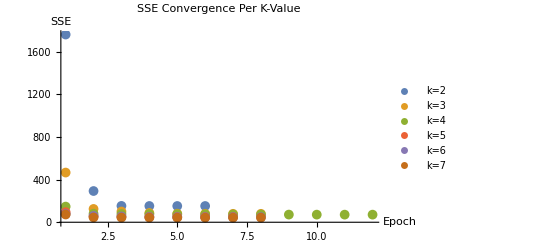

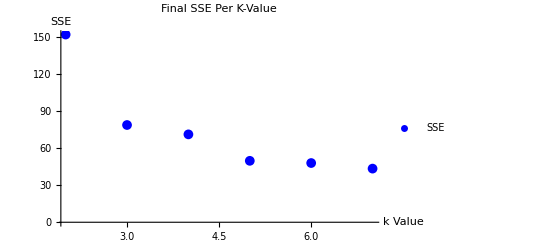

```mathematica
k2={1759.160,292.730,153.403,152.513,152.369,152.369};
k3={465.750,124.827,100.668,87.072,80.231,79.287,78.941,78.941};
k4={146.800,80.048,77.337,76.498,75.532,74.234,73.291,72.358,71.829,71.406,71.340,71.340};
k5={94.580,55.236,51.755,50.184,49.882,49.869,49.869};
k6={76.990,59.125,54.127,49.621,48.314,48.118,48.073,48.073};
k7={72.650,45.230,44.229,43.887,43.687,43.598,43.545,43.545};
all={152.369,78.941,71.340,49.869,48.073,43.545};
ks={Transpose[{Range[Length[k2]],k2}],Transpose[{Range[Length[k3]],k3}],Transpose[{Range[Length[k4]],k4}],Transpose[{Range[Length[k5]],k5}],Transpose[{Range[Length[k6]],k6}],Transpose[{Range[Length[k7]],k7}]};
ListPlot[ks,
AxesLabel->{Style["Epoch", Black],Style["SSE", Black]},PlotLabel->Style["SSE Convergence Per K-Value", Black],
PlotMarkers-> {●,10}, PlotLegends->{"k=2","k=3","k=4","k=5","k=6","k=7"}, PlotRange->All
]
ListPlot[Transpose[{Range[2,7],all}],AxesLabel->{Style["k Value", Black],Style["SSE", Black]}, PlotLabel->Style["Final SSE Per K-Value", Black], 
PlotStyle->{Blue},PlotMarkers-> {●,10}, PlotLegends->{"SSE"}, PlotRange->All]
```

Adding the instance label produces much more reliable results. Almost always each cluster will have around 49-51 instances in it. Interestingly enough, clusters above k=3 are just divisions of the k=3 clusters. at k=4, there will be two clusters of size ~50 and two clusters of size ~25. Upon investigation, the former clusters are just divisions of one of the k=3 clusters. The clusters also reliably fall along label boundaries and almost always assign the same instances to the same label-cluster.

### Part 3

The final feature in the rings data is treated continuously below. This is likely because because the amount of possible values for this feature is around 29. Because there are so many possible values, it makes more sense to use a euclidian distance-type metric rather than a mode of the features. Assuming that there is an inherent physical meaning to the final feature, a distance metric will more accurately capture the cluster than a mode because it considers more cluster instances than a mode when recalculating the cluster centroid.

As before, the convergence per k-value is shown below. It took the k=7 data set the longest to converge probably because instances in the cluster kept switching between clusters. The final SSE values are shown in the next plot. As always, a greater k-value creates clusters with instances closer to the centroid.Interestingly enough, there was very little difference between the k=6 and k=7 trials.

The unnormalized data is shown first.

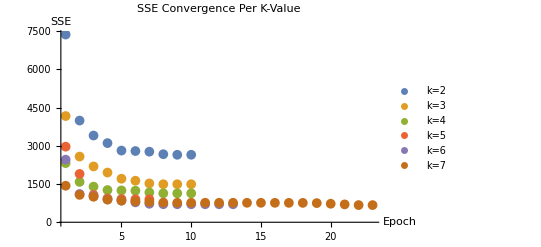

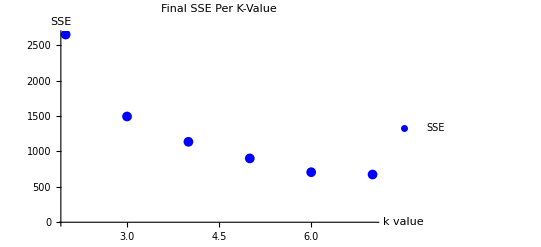

```mathematica
k2={7371.724,3993.376,3405.429,3108.459,2815.087,2797.052,2771.545,2672.586,2650.346,2650.346};
k3={4171.614,2580.061,2192.291,1952.150,1709.215,1631.266,1525.323,1493.540,1493.506,1493.506};
k4={2322.819,1585.910,1398.396,1264.923,1249.834,1239.249,1170.955,1136.023,1135.983,1135.983};
k5={2968.439,1897.561,1075.902,936.577,911.043,901.539,901.539};
k6={2458.448,1110.790,1019.406,896.374,849.600,781.373,724.904,708.787,708.017,707.565,706.932,706.587,706.587};
k7={1433.636,1075.025,1002.136,890.646,850.421,823.765,798.589,774.023,765.744,765.177,765.150,765.122,765.014,764.395,763.612,762.707,761.708,761.045,752.536,727.043,701.292,674.047,674.047};
all={2650.346,1493.506,1135.983,901.539,706.587,674.047};
ks={Transpose[{Range[Length[k2]],k2}],Transpose[{Range[Length[k3]],k3}],Transpose[{Range[Length[k4]],k4}],Transpose[{Range[Length[k5]],k5}],Transpose[{Range[Length[k6]],k6}],Transpose[{Range[Length[k7]],k7}]};
ListPlot[ks,
AxesLabel->{Style["Epoch", Black],Style["SSE", Black]},PlotLabel->Style["SSE Convergence Per K-Value", Black],
PlotMarkers-> {●,10}, PlotLegends->{"k=2","k=3","k=4","k=5","k=6","k=7"}, PlotRange->All
]
ListPlot[Transpose[{Range[2,7],all}],AxesLabel->{Style["k value", Black],Style["SSE", Black]}, PlotLabel->Style["Final SSE Per K-Value", Black], 
PlotStyle->{Blue},PlotMarkers-> {●,10}, PlotLegends->{"SSE"}, PlotRange->All]
```

The normalized data is shown next. Notice that there are some really weird behaviors with the k=2 data. This is obviously not a good fit on the data. On/after k=3, the algorithm seems to approach a more reasonable fit. In fact, after k=3 the SSE does not improve very dramatically at all. The k=3 and k=7 points are very close to each other.

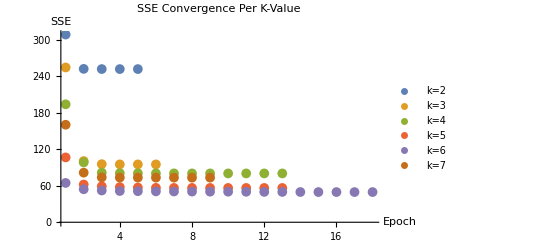

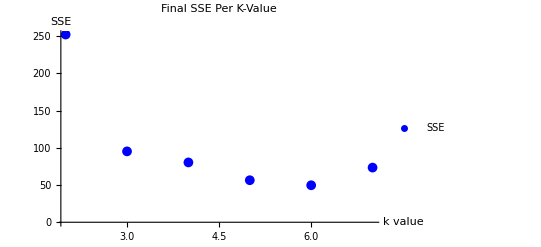

```mathematica
k2={308.946,252.450,252.152,252.118,252.118};
k3={254.781,100.688,95.621,95.240,95.211,95.211};
k4={194.121,98.521,81.773,80.808,80.614,80.524,80.445,80.405,80.392,80.372,80.358,80.354,80.354};
k5={106.714,62.122,59.169,57.831,57.163,56.678,56.538,56.529,56.512,56.482,56.460,56.457,56.457};
k6={64.695,54.326,52.274,51.421,51.121,50.818,50.647,50.485,50.346,50.285,50.159,49.960,49.890,49.767,49.721,49.693,49.683,49.683};
k7={160.493,81.631,73.873,73.534,73.458,73.437,73.426,73.420,73.420};
all={252.118,95.211,80.354,56.457,49.683,73.420};
ks={Transpose[{Range[Length[k2]],k2}],Transpose[{Range[Length[k3]],k3}],Transpose[{Range[Length[k4]],k4}],Transpose[{Range[Length[k5]],k5}],Transpose[{Range[Length[k6]],k6}],Transpose[{Range[Length[k7]],k7}]};
ListPlot[ks,
AxesLabel->{Style["Epoch", Black],Style["SSE", Black]},PlotLabel->Style["SSE Convergence Per K-Value", Black],
PlotMarkers-> {●,10}, PlotLegends->{"k=2","k=3","k=4","k=5","k=6","k=7"}, PlotRange->All
]
ListPlot[Transpose[{Range[2,7],all}],AxesLabel->{Style["k value", Black],Style["SSE", Black]}, PlotLabel->Style["Final SSE Per K-Value", Black], 
PlotStyle->{Blue},PlotMarkers-> {●,10}, PlotLegends->{"SSE"}, PlotRange->All]
```

### Part 4

Below are the requested plots showing the silhouette metric on the abalone data set. The first plot shows how many epochs it took for each k-value to converge. The second plot shows the final average silhouette per k-value. higher silhouettes were found at k values of 3 and 6. The lowest silhouette score was found at 5. It makes sense that the highest silhouette scores were found at multiples of each other. This is probably the case with every multiple of the natural cluster. The data set is probably naturally clustered into 3 clusters and the silhouette score reflects that with higher silhouettes at 3 and 6. Splitting 3 clusters into 2 each will still result in a good silhouette because of the even division. In this way, the silhouette score is much better than anything else to decide which cluster size to use. It shows which k-values are optimal quite easily.

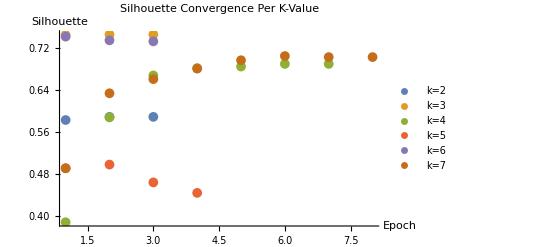

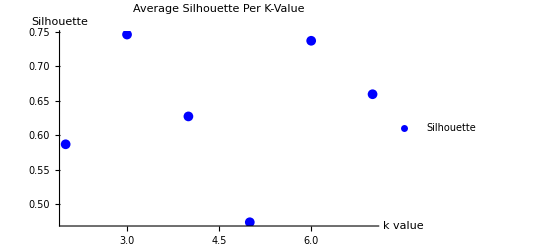

```mathematica
k2={0.583,0.589,0.589};
k3={0.745,0.746,0.746};
k4={0.388,0.588,0.668,0.682,0.685,0.690,0.690};
k5={0.491,0.498,0.464,0.444};
k6={0.742,0.735,0.733};
k7={0.491,0.634,0.661,0.681,0.697,0.705,0.703,0.703};
all={Mean[k2],Mean[k3],Mean[k4],Mean[k5],Mean[k6],Mean[k7]};
ks={Transpose[{Range[Length[k2]],k2}],Transpose[{Range[Length[k3]],k3}],Transpose[{Range[Length[k4]],k4}],Transpose[{Range[Length[k5]],k5}],Transpose[{Range[Length[k6]],k6}],Transpose[{Range[Length[k7]],k7}]};
ListPlot[ks,
AxesLabel->{Style["Epoch", Black],Style["Silhouette", Black]},PlotLabel->Style["Silhouette Convergence Per K-Value", Black],
PlotMarkers-> {●,10}, PlotLegends->{"k=2","k=3","k=4","k=5","k=6","k=7"}, PlotRange->All
]
ListPlot[Transpose[{Range[2,7],all}],AxesLabel->{Style["k value", Black],Style["Silhouette", Black]}, PlotLabel->Style["Average Silhouette Per K-Value", Black], 
PlotStyle->{Blue},PlotMarkers-> {●,10}, PlotLegends->{"Silhouette"}, PlotRange->All]
```

### Part 4

For my expansion project, I designed ways to select starting centroids. The function is applied to the entire data set one column (feature) at a time. The next few paragraphs describe this algorithm assuming a cluster amount of k:
For continuous features the set of all possible values is sorted and divided into k+1 portions. Each boundary instance is then sequestered to be used as a centroid.
For nominal features, the set of features is sorted and the features with more instances are shown first. the data is then divided into k+1 even portions again and the boundary instances are used as centroids.
For unknown values, features are discarded unless more than 2/(k+1) times the total size of the data set is unknown. At this point, some centroids will be calculated as unknown until there centers are re-assigned.

What I found is that there was no improvement using this method over a normal randomization Initialization. Below is a comparison between the randomization and this new method using the un-normalized abalone data set:

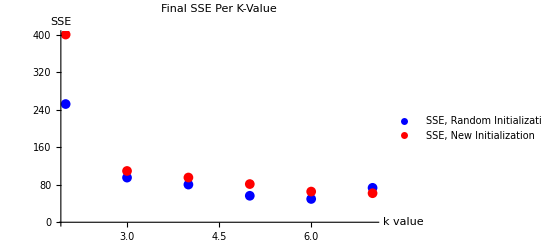

```mathematica
all={252.118,95.211,80.354,56.457,49.683,73.420};
new={400.345, 109.386, 95.39776,81.453,65.438,61.927};
ListPlot[{Transpose[{Range[2,7],all}], Transpose[{Range[2,7],new}]},AxesLabel->{Style["k value", Black],Style["SSE", Black]}, PlotLabel->Style["Final SSE Per K-Value", Black], 
PlotStyle->{Blue, Red},PlotMarkers-> {●,10}, PlotLegends->{"SSE, Random Initialization", "SSE, New Initialization"}, PlotRange->All]
```

The reason this showed no improvement was likely because the centroids it calculated were not actually part of the dataset. The combination of columns were so wrong that it was no better than random assignment. It took no consideration of associated features and whether the resulting centroid was even near the rest of the data.

In an attempt to make an initialization algorithm that worked, I next created an algorithm that chose instances based on how far they were from each other. Under this method, the program would take the entire dataset and calculate the distance between each instance and every other instance. It would then pick the two furthest-away points. This worked great for two clusters, but I couldn’t figure out what to do for more clusters. Somehow I would need to calculate the instance that maximized the distance from the initial two, but I couldn’t figure out a good way to do this. Besides, it was already decently slow for two clusters.